# UndirectedGraphToMixedGraph

Change an undirected graph into a mixed graph

## Definition

```mathematica
ClearAll[UndirectedGraphToMixedGraph]
UndirectedGraphToMixedGraph[graph_?GraphQ,threshold_]:=Block[{replaceCount} ,replaceCount=Floor[threshold EdgeCount[graph]];Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,graph,RandomSample[EdgeList[graph],replaceCount]],EdgeWeight->Thread[EdgeList[graph]->(AnnotationValue[{graph,#1},EdgeWeight])&/@EdgeList[graph]]]]/;0<=threshold<=1
```

## Documentation

### Usage

UndirectedGraphToMixedGraph[graph, frac]

randomly replaces a fraction frac of graph's undirected edges with directed edges.

### Details & Options

A mixed graph is one with both directed and undirected edges. UndirectedGraphToMixedGraph takes the undirected input graph and produces a mixed graph by replacing a random sample of graph's edges with randomly-oriented directed edges.

The input frac should be a number between 0 and 1 that determines the fraction of undirected edges which are coverted to directed edges. A frac value of 0 returns the original graph. A frac value of 1 produces a fully-directed graph (with randomly-oriented edges). A frac value of 0.5 would make approximately 50% of the edges directed.

## Examples

### Basic Examples

Make a parametric Harary graph mixed:

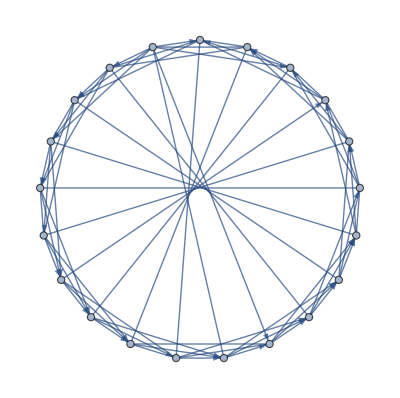

```mathematica
UndirectedGraphToMixedGraph[HararyGraph[7,21],.5]
```

Construct a circulant graph with 35% directed edges:

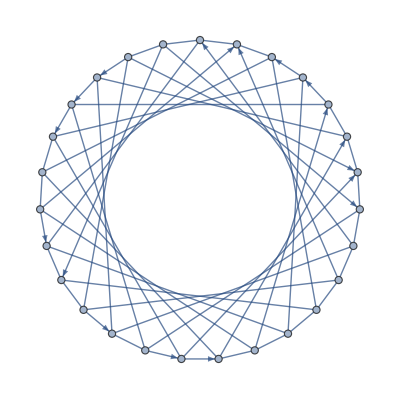

```mathematica
UndirectedGraphToMixedGraph[CirculantGraph[27,{1,8}],0.35]
```

Generate a random spatial graph and take the largest connected component by edge count:

```mathematica
𝒢=Graph[First[TakeLargestBy[ConnectedGraphComponents@RandomGraph[SpatialGraphDistribution[148,ⅇ^-2]],EdgeCount,1]],ImageSize->Full]
```

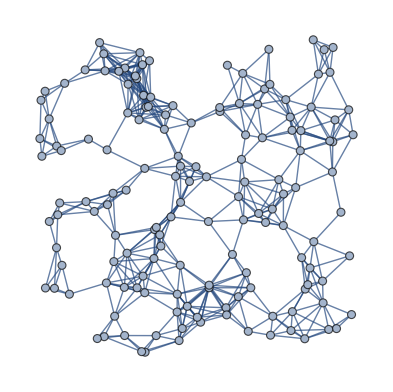

Make the graph mixed with 50% directed edges:

```mathematica
Graph[UndirectedGraphToMixedGraph[𝒢,.5],ImageSize->Full]
```

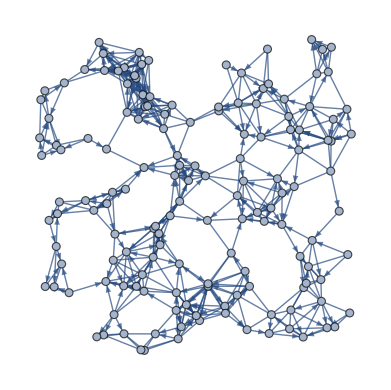

### Applications

Create a mixed dodecahedral graph with about 50% directed edges:

```mathematica
dodecahedralGraph=UndirectedGraphToMixedGraph[GraphData["DodecahedralGraph"],.5];
```

Find a Hamiltonian cycle if it exists:

```mathematica
FindHamiltonianCycle[UndirectedGraphToMixedGraph[dodecahedralGraph,.5]]
```

{}

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

graph

directed graph

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

RandomGraph

SpatialGraphDistribution

### Related Resource Objects

OrientedGraphQ

TransitiveGraphQ

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.